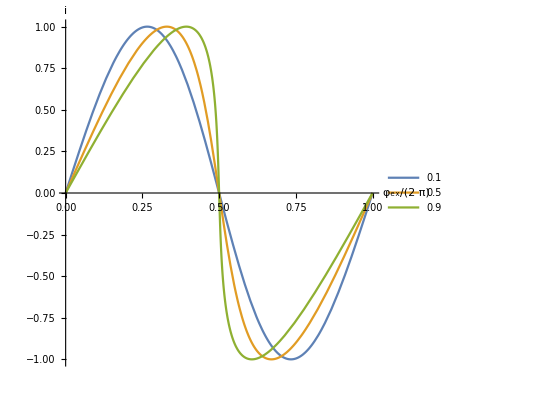

```mathematica
lq={0.1,0.5,0.9};
phix1[phi_]:=phi+lq[[1]]*Sin[phi];
phix2[phi_]:=phi+lq[[2]]*Sin[phi];
phix3[phi_]:=phi+lq[[3]]*Sin[phi];
iout1[phi_]:=(phix1[phi]-phi)/lq[[1]];
iout2[phi_]:=(phix2[phi]-phi)/lq[[2]];
iout3[phi_]:=(phix3[phi]-phi)/lq[[3]];
ParametricPlot[{{phix1[phi]/(2Pi),iout1[phi]},{phix2[phi]/(2Pi),iout2[phi]},{phix3[phi]/(2Pi),iout3[phi]}},{phi,0,2Pi},
AspectRatio->1, PlotLegends->{"0.1","0.5","0.9"},AxesLabel->{"φ_ex/(2  π)","i"}]
```

```mathematica
lq1=3;
U[phi_]:=(1-Cos[phi])+(phi-phx)^2/(2*lq1);
Animate[Plot[(1-Cos[phi])+(phi-phx)^2/(2*lq1),{phi, -3Pi, 3Pi },PlotRange->{{-3Pi,3Pi},{-5,8}},PlotLabel->"= φ_ex/2π"phx /(2Pi),AxesLabel->{"φ","(U (φ))/E_J"} ],{phx,0,2Pi},AnimationRunning->False]
```

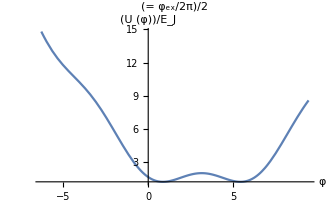

```mathematica
lq1=3;phx1=Pi;
U[phi_]:=(1-Cos[phi])+(phi-phx1)^2/(2*lq1);
Plot[(1-Cos[phi])+(phi-phx1)^2/(2*lq1),{phi, -2Pi, 3Pi },PlotRange->All,PlotLabel->"= φ_ex/2π"phx1 /(2Pi),AxesLabel->{"φ","(U (φ))/E_J"} ]
```